## Maximization using Lagrange multipliers An analytic approach

General instructions: 

1. To evaluate Mathematica code, get the cursor in the cell containing the code and his Shift+Enter.

2. Read the review and the description of the technique used to find extrema. The problems are written at the end of the notebook in a section entitled: Problems.  That section should be copied into a new Mathematica notebook. Your answers will be put in the new notebook.

3. Do not write Mathematica code and text in the same cell. In the cells where you are writing text, you need to format the cell for text. You can use the Format/Style/Text from the bar above, or Alt+7 to format it for text. You don’t need to format it for code.

4. This will be due on Friday, April 29. Please put a .pdf copy of your solutions on Canvas.

## Review:

#### In the last section, we used pictures to approximate the maximum and minimum values of a function f(x,y) on a constraint curve described by an equation C(x,y)=c. The picture we looked at had two things going on in it: 1. A graph of the constraint equation: C(x,y)=c. This was the red curve in those picture. The question was: of all of the points on this curve, which gives the biggest output and which gives the smallest output. 2. A conour plot of a bunch of level curves for the function f(x,y). If a level curve of f(x,y) corresponding to some number k cut across the constraint curve, we suspected that k was not an extreme value of f. These two points led to the Key Graphical Observation. ##What was it?

## An analytical approach:

In this section, we will develop a process by which we can turn the question of extreme values into solving a system of equations. The key will be the gradient. Why is that they key? The following fact is the point that we will exploit.

Gradients vis-a-vis level sets: The gradient of a function f takes value in the domain of f. The level sets of f also live in the domain of f. The gradient at any point in the domain is normal (perpendicular) to the level set on which it lies. 

A quicker way of saying this is: Gradients are tangent to level sets.

Let’s look at two curves that are tangent at a point and take a look at the gradients of each. Consider the graph cubic polynomial y=x^3-2x+3 (blue) and the hyperbola -6 x^2+3 y^2=6 (red).

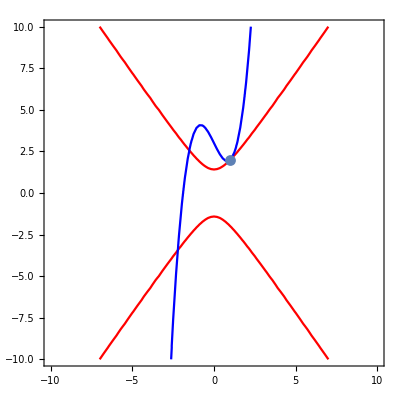

```mathematica
Show[ContourPlot[-6 x^2+3 y^2==6,{x,-10,10},{y,-10,10},ContourStyle->Red],
	ContourPlot[x^3-2x-y==-3,{x,-10,10},{y,-10,10},ContourStyle->Blue],ListPlot[{{1,2}}]]
```

These curves meet at three different points. We are interested in the point (1,2) at which they are tangent. Here’s a picture that has been zoomed in near that point of tangency. Also, we will put in their common tangent line.

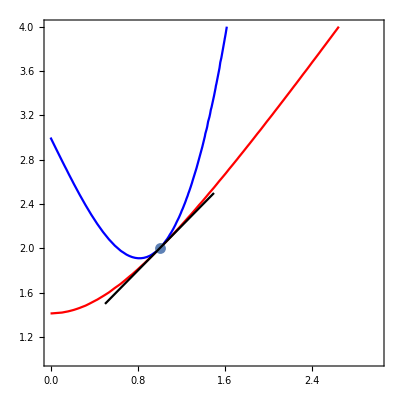

```mathematica
Show[ContourPlot[-6 x^2+3 y^2==6,{x,0,3},{y,1,4},ContourStyle->Red],
	ContourPlot[x^3-2x-y==-3,{x,0,3},{y,1,4},ContourStyle->Blue],ListPlot[{{1,2}}],
ContourPlot[y==x+1,{x,.5,1.5},{y,1.5,2.5},ContourStyle->Black]]
```

We want to consider these curves as level sets, so we can talk about their gradients. To that end, let C(x,y)=-6 x^2+3 y^2 and let f(x,y)=x^3-2x-y. Then the red curve is the level set of C corresponding to the level 6; and, the blue curve is the level set of f corresponding to the level -3. Now, we know the gradients of these two functions, C and f are both going to be normal to that black tangent line. At first blush, one might think that this means that they need to be the same. However, the story is a little more subtle than that.

To see this, we will add gradients to the picture. Here are the formulas for the gradient vectors: ∇C(x,y)=<-12x,6y> and ∇f(x,y)=<3 x^2-2,-1>. Plugging in the point of tangency (1,2), we get the following two gradient vectors: ∇C(1,2)=<-12,12> and ∇f(1,2)=<1,-1>. Let’s add these to our picture:

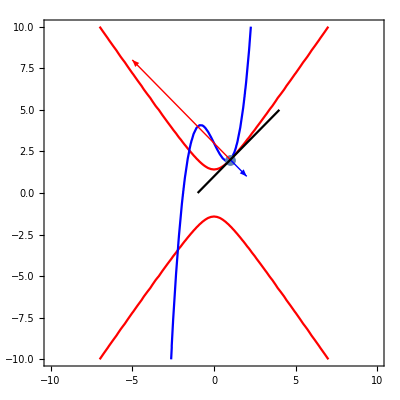

```mathematica
Show[ContourPlot[-6 x^2+3 y^2==6,{x,-10,10},{y,-10,10},ContourStyle->Red],
	ContourPlot[x^3-2x-y==-3,{x,-10,10},{y,-10,10},ContourStyle->Blue],ListPlot[{{1,2}}],
	Graphics[{Red,Arrow[{{1,2},{-5,8}}]}],
Graphics[{Blue,Arrow[{{1,2},{2,1}}]}],
ContourPlot[y==x+1,{x,-2,4},{y,0,6},ContourStyle->Black]]
```

(To keep the picture contained, I scaled the red vector down by a factor of 2). Now, we see the whole story. Since the two curves share a common tangent line at the point (1,2), the two gradients need not be the same vector, but they must be parallel. So, one will be a scalar multiple of the other. In our case, since ∇C(1,2)=<-12,12> and ∇f(x,y)=<1,-1>, we see ∇C(1,2)=-12∇f(1,2). The number -12 in this context is called a LaGrange multiplier.

The logic behind the process:

Let’s suppose that the maximum (or minimum) value for the function f on the curve C is the number k and that this occurs at the point (x_0,y_0). Lastly, assume that the curve C is described by an equation of the form C(x,y)=c.

1. Then, in most cases, the level set for f is tangent to the curve C at the point (x_0,y_0).
2. So, at this point, ∇f is parallel to ∇C .
3. This means that there is a real number λ so that ∇f =λ ∇C(x_0,y_0). That is to say, <f_x(x_0,y_0),f_y(x_0,y_0)>=<λC_x(x_0,y_0),λC_y(x_0,y_0)> .
4. This means, the following equations are all satisfied:
		i. C(x_0,y_0)=c
		ii. f_x(x_0,y_0)=λC_x(x_0,y_0)
		iii. f_y(x_0,y_0)=λC_y(x_0,y_0)
		iv. f(x_0,y_0)=k

If you look at these four equations, you will notice that there are four unknowns, namely, x_0, y_0, λ and k. Moreover, k only appears in the last one. So, the process is to solve the first three equations for x_0, y_0 and λ. We might have several solutions for the pair (x_0,y_0). However, it is true that any extrema will happen at such a point. So, if we get several answers, we just plug them all in to find the max and the min.

If you are a careful reader, you will have noticed the word “most” that appears in the first item doesn’t appear in the above paragraph. That is because the only exceptions to the tangency critereon happen when the gradient of f is <0,0>. In such cases, solving the system of equations will yield a soultion with λ=0.

## An example:

Now, let’s work through the problem we studied in the last technology assignment where we had been looking at the graph. Recall, what the question is:

#### Find the extrema of f(x,y)=3x-4y on the circle x^2+y^2=25.

#### Here, our constraint function is C(x,y)=x^2+y^2, c=25 and the function that we want the extrema of is f(x,y)=3x-4y. We need to solve the following system of equations for x, y and λ. C(x,y)=c f_x(x,y)=λC_x(x,y) f_y(x,y)=λC_y(x,y) In this case, that is the system of equations: x^2+y^2=25 3=λ(2x) -4=λ(2y)

To solve this system, we could take out a pen and paper (in fact, we should be able to do it that way), but hey, we’re sitting at a computer.

```mathematica
NSolve[x^2+y^2==25&&3==λ*2x&&-4==λ*2y,{x,y,λ}]
```

{{x→-3.,y→4.,λ→-0.5},{x→3.,y→-4.,λ→0.5}}

We see we got two answers: (x,y)=(-3,4) and (x,y)=(3,-4). To find the corresponding values of f, we could plug these points in. Or, better yet, let’s adapt that bit last code to also tell us the outputs (which I’ll call k).

```mathematica
NSolve[x^2+y^2==25&&3==λ*2x&&-4==λ*2y&&3x-4y==k,{x,y,λ,k}]
```

{{x→-3.,y→4.,λ→-0.5,k→-25.},{x→3.,y→-4.,λ→0.5,k→25.}}

Now we have our answer: f achieves its minimum at (-3,4), and its value there is -25; f achieves its maximum at (3,-4), and its value there is 25.

## Another example:

Here’s another question we answered in the previous technology assignment:

  A question: Use a picture to approximate the extreme values for f(x,y)=4 x^2+9 y^2 on the constraint curve C: xy=4
  
  We can now answer it without a picture and without approximating

#### We need to solve the following system of equations for x, y and λ. C(x,y)=c f_x(x,y)=λC_x(x,y) f_y(x,y)=λC_y(x,y) In this case: xy=4 8x=λ(y) 18y=λ(x) Here’s the code that does it:

```mathematica
NSolve[x*y==4&&8x==λ*y&&18y==λ*x&&4 x^2+9 y^2==k,{x,y,λ,k}]
```

{{x→-2.44949,y→-1.63299,λ→12.,k→48.},{x→0.-2.44949 ⅈ,y→0.+1.63299 ⅈ,λ→-12.,k→-48.+0. ⅈ},{x→0.+2.44949 ⅈ,y→0.-1.63299 ⅈ,λ→-12.,k→-48.+0. ⅈ},{x→2.44949,y→1.63299,λ→12.,k→48.}}

Now that’s a bit of a mess. Mathematica didn’t realize I was only interested in real answers and it gave me some complex solutions. There’s a fix:

```mathematica
NSolve[x*y==4&&8x==λ*y&&18y==λ*x&&4 x^2+9 y^2==k,{x,y,λ,k},Reals]
```

{{x→-2.44949,y→-1.63299,λ→12.,k→48.},{x→2.44949,y→1.63299,λ→12.,k→48.}}

So, the extreme value is 48 (which is pretty close to our approximation of 47.975). We still need to decide whether this is a max or a min. Now, we could draw the picture we have above. Or we can plug in another point on the curve and compare. Note that (2,2) is on our constraint curve and that f(2,2)=52. Moreover, as our curve wanders off to infinity, one of the coordinates gets close to 0 and the other gets pretty big. Plugging a point like that into f will give a pretty big output. So, 48 must be a minimum.

## Some notes on the process

1. Like the process you used in Calc A to find extrema of a function of one variable, what we get from the process of Lagrange multipliers is a collection of points, which we call critical points. The theory says that the maximum and minimum values each occur at a critical point, not that every critical point yields a max or a min. So, the process, in effect, reduces the problem of checking all the points on the curve to checking a handful of them. Even though the process is incomplete in this sense, it should still be seen as a great step forward.

2. The constraint curve we worked on in the first example above was a bounded boundariless curve (a complete circle), meaning a curve without endpoints. If instead the constraint curve has endpoints (for example when the constraint curve is a line segment), those endpoints should be considered critical points and tested with along with those points where the level set is tangent to the constraint curve. In the case where the curve goes on forever, we need to understand what is happening to points on the curve as they get further and further out.  

3.  The theory was developed assuming the that values from one side of a level set are less those from the other. You should be relieved to learn that the process described above still works in the exceptional cases that we have been alluding to. The exceptional cases can only occur when the gradient is the zero vector. The process above gives us those points on the constraint curve where the gradient is zero as solutions that have λ=0.

4. The student with foresight has probably already figured out that this can be done in higher dimensions. In the case of a function of 3-variables, our level sets are surfaces in ℝ^3. A straightforward generalization of our in general statement holds true. Here we take our constraint to be equations in three variables. The constraint describes a constraint surface instead of a constraint curve. The process finds those points where the level set is tangent to the constraint surface. Problems get really hard when the constraint surface has a boundary because such a boundary has infinitely many points. There are processes to deal with such cases, but we will only consider constraint surfaces without boundary.

## Your assignment: Problems

This will be due on Friday, April 29

General instructions:
A. Copy the Your Assignment section into a new Mathematica notebook.
B. Place the answer to a question right after it. 
C. Remember to use alt+7 to format cells in which you will be typing text. You don’t need to format cells in which you will be writing Mathematica code.

To submit
D. Save the notebook as yourname_assignment 2.nb
E. Evaluate entire notebook.
F. Save as a .pdf file.
G. Submit to Canvas

## What was the key graphical observation from Technology Assignment 2?

## Some of these exercises come out of Rogowski’s text. In each, you are given a function f and a constraint curve C. For each:

1. Write a system of equations involving Lagrange multipliers whose solutions include the critical points.
2. Use NSolve (DO NOT FORGET THE DOUBLE EQUAL SIGNS ==) to solve that system of equations.
3. Find the max and min for f given the constraint C. (Don’t just give me the NSolve output. Tell me the point that gives the max and what the max is. Same for the min.)  Remember, for this to use Alt+7 when you type text. 

A. f(x,y)=5x-2y;              	C: x^2+y^2=9
B. f(x,y)=x^4 y^2                   	C: x^2+2 y^2=6
C. f(x,y)=(10x+100)/y        	C:x^2+(y-8)^2=1
D. f(x, y) = 4 x^2 - 9 y^2  	C: (x+2)^2-2y=11
E. f(x,y,z)=xy+4z                        C: x^2+2 y^2+3 z^2=6
F. f(x,y,z)=7x+3y-z             C: x+y=√(75+4(x-y)^2+z^2)

## Which point on the ellipse 4 x^2+25 y^2=49 is closest to the point (2,1)? Which is furthest? Explain.

## The corner of a building makes a 60^o angle. An architect wants to put fence outside the building around this corner to make a playground. The corner of the building will come into the playground (as in the picture below). He has 135 feet of fencing with which to work. What dimensions will maximize the area of the playground? How far from the corner of the bulding will he need to anchor the fence?

Bonus: 

1. Referring to part B, let P be the point on the ellipse which is closest to the point (2,1) and let Q be the furthest. Show that the vector from (2,1) to P and the vector from (2,1) to Q are both normal to the ellipse. Show that these are the only two points on the ellipse that have this property. In your own words, describe what you think is going on here.   

2. What are the level sets and what is the constraint surface in the last problem in Part A? Get a good picture describing what is going on.